## Setup

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,ListLogPlot,LogLinearPlot,Histogram,DensityHistogram,ListStepPlot},Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

```mathematica
myLog[x_]:={x[[1]],x[[2]],Log[x[[3]]]}
```

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/usr/bin/xelatex","Ghostscript"->"/usr/bin/gs"];
myMaTeX[x_]:= MaTeX[x,"Preamble"->{"\\usepackage{fontspec}","\\setmainfont{DejaVu Serif}"},FontSize->16]
```

```mathematica
myMaTeX2[x_]:= MaTeX[x,FontSize->18]
```

## Load params & Test

```mathematica
particle="Upsilon";
centrality="minbias";
```

```mathematica
myParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../input/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&];
myDict=Association[Table[If[StringContainsQ[myParams[[i,2]],","],myParams[[i,1]]->ToExpression/@StringSplit[myParams[[i,2]],","],myParams[[i,1]]->ToExpression[myParams[[i,2]]]],{i,1,Length[myParams]}]]
```

<|A→208,collisionType→1,particleType→0,alphas→1,lambdaQCD→0.308,qhat0→0.075,useCentrality→0,centralityEdges→{0,20,40,60,100},lp→1.5,massp→0.938,rootsnn→5023,Ny→21,Npt→81,y_min→-5.,y_max→5.,ptmin→0.1,ptmax→40.1|>

```mathematica
(* load variables from params file to automate some things below *)
roots = myDict["rootsnn"]
```

5023

```mathematica
roots=5023;
```

```mathematica
M =If[ myDict["particleType"]==0,9.45,3.43](*0 for JPsi and 1 for Upsilon*)
```

9.45

```mathematica
cE = Which[roots==5023,"5.02",roots==8160,"8.16"]
```

5.02

```mathematica
centEdges=myDict["centralityEdges"]
centBins=Transpose[{Drop[centEdges,-1],Drop[centEdges,1]}]
centTags=centBins/. {a_,b_}:>ToString@Row[{a,"-",b}]
```

{0,20,40,60,100}

{{0,20},{20,40},{40,60},{60,100}}

{0-20,20-40,40-60,60-100}

### General functions

```mathematica
Mperp2[pt_] = pt^2+M^2; (* GeV ^2 *)
Mperp[pt_] = Sqrt[Mperp2[pt]]; (* GeV *)
ymaxFunction[pt_] = Log[roots/Mperp[pt]];
ptmaxFunction[y_]=Sqrt[(roots Exp[-y])^2 - M^2];
```

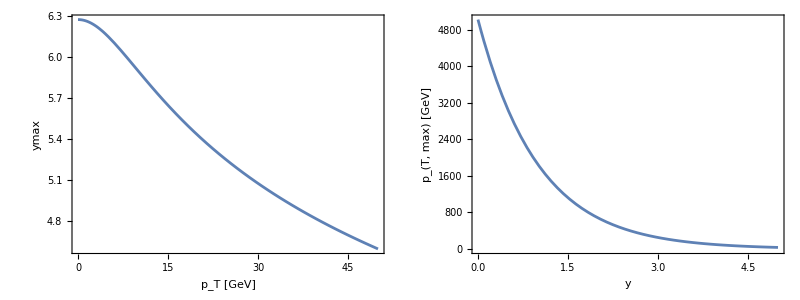

```mathematica
Grid[{{Plot[ymaxFunction[pt],{pt,0,50},FrameLabel->{"p_T [GeV]","ymax"}],Plot[ptmaxFunction[y],{y,0,5},FrameLabel->{"y","p_(T, max) [GeV]"}]}}]
```

## Read & Plot Data

### Read pA data

```mathematica
pAresultLog=Interpolation[myLog/@Import[wd<>"/../output/"<>particle<>"/minbias_"<>particle<>"_pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pAerrorLog=Interpolation[myLog/@Import[wd<>"/../output/"<>particle<>"/minbias_"<>particle<>"_pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pAresultLog[[1,1]]
{ptmin,ptmax} = pAresultLog[[1,2]]
pAresult[y_,pt_]:=Exp[pAresultLog[y,pt]]
pAerror[y_,pt_]:=Exp[pAerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
Plot3D[pAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[pAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read pp data

```mathematica
ppresultLog=Interpolation[myLog/@Import[wd<>"/../output/"<>particle<>"/minbias_"<>particle<>"_pp-cross-section.tsv"],InterpolationOrder->Automatic];
ppresult[y_,pt_]:=Exp[ppresultLog[y,pt]]
```

```mathematica
Plot3D[ppresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read RpA data

```mathematica
RpAresult=Interpolation[Import[wd<>"/../output/"<>particle<>"/minbias_"<>particle<>"_RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpAerror=Interpolation[Import[wd<>"/../output/"<>particle<>"/minbias_"<>particle<>"_RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpAresult[[1,1]];
{ptmin,ptmax} =RpAresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
mainPlot=Plot3D[RpAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Automatic,PlotRange->{0,1.5}];
(*Plot the plane at z=1*)
planePlot=Plot3D[1,{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Opacity[0.5,Red],Mesh->None];
Show[mainPlot,planePlot]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpAresultU[y_,pt_]=RpAresult[y,pt]+RpAerror[y,pt];
RpAresultL[y_,pt_]=RpAresult[y,pt]-RpAerror[y,pt];
```

```mathematica
mypAPlotY[pt_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,2.0}]
mypAPlotPT[y_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,2.0}]
```

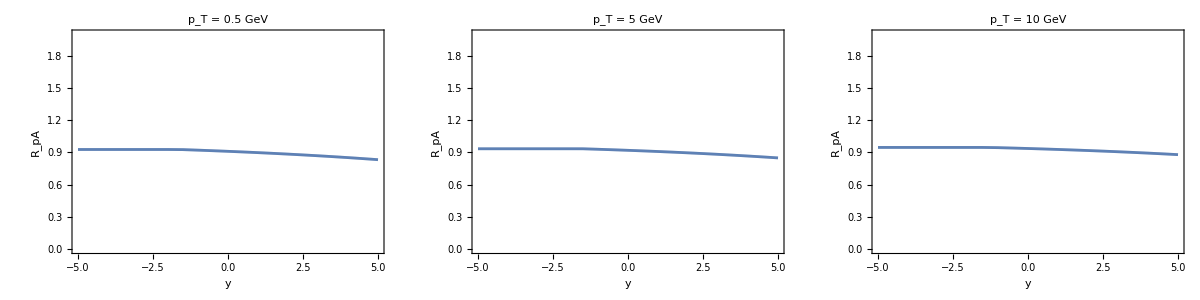

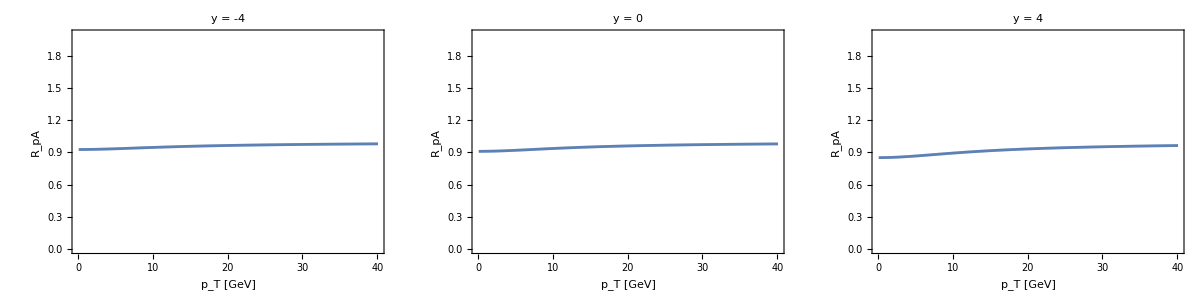

```mathematica
Grid[{{mypAPlotY[0.5],mypAPlotY[5],mypAPlotY[10]}}]
Grid[{{mypAPlotPT[-4],mypAPlotPT[0],mypAPlotPT[4]}}]
```

## RpA vs y & pT binned Plots

### Rapidity Dependent (p_T averaged)

```mathematica
ptmin = 0.1;
ptmax = 20;
```

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultPTavg[{ymin_,ymax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ybins = -5 + 0.5Range[0,20]
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
binnedRPAelossVSY = RpAresultPTavg/@ Transpose[{Drop[ybins,-1],Drop[ybins,1]}];
```

```mathematica
binnedRPAElossDataVSY = Transpose[{Drop[ybins,-1],binnedRPAelossVSY}]
```

{{-5.,0.953508},{-4.5,0.953508},{-4.,0.953508},{-3.5,0.953508},{-3.,0.953508},{-2.5,0.953508},{-2.,0.953487},{-1.5,0.95287},{-1.,0.950709},{-0.5,0.947364},{0.,0.943709},{0.5,0.939817},{1.,0.935681},{1.5,0.931284},{2.,0.926611},{2.5,0.921649},{3.,0.916385},{3.5,0.910798},{4.,0.904875},{4.5,0.897616}}

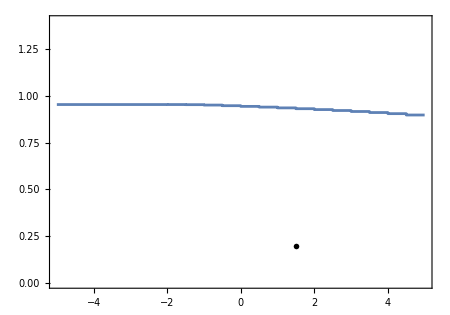

```mathematica
rapidityplot=ListStepPlot[binnedRPAElossDataVSY,Right,PlotRange->{{-5,5},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ptmin]<>"<$p_T$<"<>ToString[ptmax]<>" GeV }"],{1.5,0.2}]}]
```

```mathematica
RpAresultPTavg[{-5,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.937695

### p_T Dependent: Forward(1 = 1.5 < y < 4, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{1.5,4},Length[myPTBins]]
```

{{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

4

1.5

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{1.5,4,0.,2.5},{1.5,4,2.5,5.},{1.5,4,5.,7.5},{1.5,4,7.5,10.},{1.5,4,10.,12.5},{1.5,4,12.5,15.},{1.5,4,15.,17.5},{1.5,4,17.5,20.},{1.5,4,20.,22.5},{1.5,4,22.5,25.},{1.5,4,25.,27.5},{1.5,4,27.5,30.},{1.5,4,30.,32.5},{1.5,4,32.5,35.},{1.5,4,35.,37.5},{1.5,4,37.5,40.},{1.5,4,40.,42.5},{1.5,4,42.5,45.},{1.5,4,45.,47.5},{1.5,4,47.5,50.}}

```mathematica
binnedRPAelossVSPT1 =RpAresultAvg/@myBins1
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.874813,0.881488,0.89221,0.904021,0.91513,0.924861,0.933132,0.940095,0.945959,0.95092,0.955146,0.958775,0.961914,0.964647,0.96705,0.969171,0.971127,0.973086,0.975043,0.977001}

```mathematica
binnedRPAelossDataVSPT1  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT1}]
```

{{0.,0.874813},{2.5,0.881488},{5.,0.89221},{7.5,0.904021},{10.,0.91513},{12.5,0.924861},{15.,0.933132},{17.5,0.940095},{20.,0.945959},{22.5,0.95092},{25.,0.955146},{27.5,0.958775},{30.,0.961914},{32.5,0.964647},{35.,0.96705},{37.5,0.969171},{40.,0.971127},{42.5,0.973086},{45.,0.975043},{47.5,0.977001}}

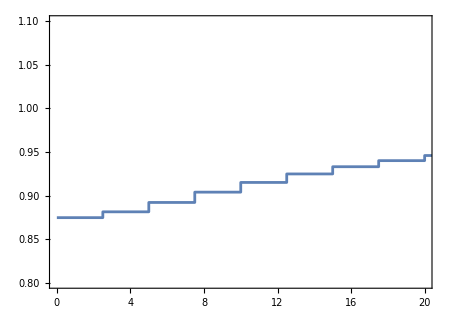

```mathematica
forwardplot= ListStepPlot[binnedRPAelossDataVSPT1,Right,PlotRange->{{0,20},{0.8,1.1}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Backward(2 = -5 < y < -2.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-5,2.5},Length[myPTBins]]
```

{{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-5,2.5,0.,2.5},{-5,2.5,2.5,5.},{-5,2.5,5.,7.5},{-5,2.5,7.5,10.},{-5,2.5,10.,12.5},{-5,2.5,12.5,15.},{-5,2.5,15.,17.5},{-5,2.5,17.5,20.},{-5,2.5,20.,22.5},{-5,2.5,22.5,25.},{-5,2.5,25.,27.5},{-5,2.5,27.5,30.},{-5,2.5,30.,32.5},{-5,2.5,32.5,35.},{-5,2.5,35.,37.5},{-5,2.5,37.5,40.},{-5,2.5,40.,42.5},{-5,2.5,42.5,45.},{-5,2.5,45.,47.5},{-5,2.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

2.5

-5

```mathematica
binnedRPAelossVSPT2 =RpAresultAvg/@myBins1
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.916276,0.920682,0.927737,0.935478,0.942763,0.949151,0.954577,0.959128,0.962965,0.96622,0.968998,0.971391,0.97267,0.976004,0.977544,0.978906,0.980176,0.981455,0.982738,0.984019}

```mathematica
binnedRPAelossDataVSPT2  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT2}]
```

{{0.,0.916276},{2.5,0.920682},{5.,0.927737},{7.5,0.935478},{10.,0.942763},{12.5,0.949151},{15.,0.954577},{17.5,0.959128},{20.,0.962965},{22.5,0.96622},{25.,0.968998},{27.5,0.971391},{30.,0.97267},{32.5,0.976004},{35.,0.977544},{37.5,0.978906},{40.,0.980176},{42.5,0.981455},{45.,0.982738},{47.5,0.984019}}

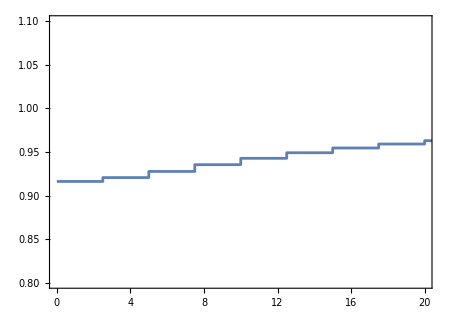

```mathematica
backwardplot=ListStepPlot[binnedRPAelossDataVSPT2,Right,PlotRange->{{0,20},{0.8,1.1}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Mid(3 = -1.93 < y < -1.93, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-1.93,1.93},Length[myPTBins]]
```

{{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-1.93,1.93,0.,2.5},{-1.93,1.93,2.5,5.},{-1.93,1.93,5.,7.5},{-1.93,1.93,7.5,10.},{-1.93,1.93,10.,12.5},{-1.93,1.93,12.5,15.},{-1.93,1.93,15.,17.5},{-1.93,1.93,17.5,20.},{-1.93,1.93,20.,22.5},{-1.93,1.93,22.5,25.},{-1.93,1.93,25.,27.5},{-1.93,1.93,27.5,30.},{-1.93,1.93,30.,32.5},{-1.93,1.93,32.5,35.},{-1.93,1.93,35.,37.5},{-1.93,1.93,37.5,40.},{-1.93,1.93,40.,42.5},{-1.93,1.93,42.5,45.},{-1.93,1.93,45.,47.5},{-1.93,1.93,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.93

-1.93

```mathematica
binnedRPAelossVSPT3 =RpAresultAvg/@myBins1
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.911125,0.91599,0.923736,0.932187,0.940109,0.94703,0.952878,0.957744,0.961832,0.965291,0.968238,0.970765,0.972927,0.974807,0.976459,0.977921,0.979269,0.980617,0.981963,0.983311}

```mathematica
binnedRPAelossDataVSPT3  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT3}]
```

{{0.,0.911125},{2.5,0.91599},{5.,0.923736},{7.5,0.932187},{10.,0.940109},{12.5,0.94703},{15.,0.952878},{17.5,0.957744},{20.,0.961832},{22.5,0.965291},{25.,0.968238},{27.5,0.970765},{30.,0.972927},{32.5,0.974807},{35.,0.976459},{37.5,0.977921},{40.,0.979269},{42.5,0.980617},{45.,0.981963},{47.5,0.983311}}

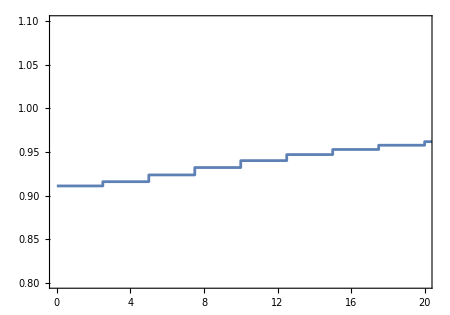

```mathematica
centralplot=ListStepPlot[binnedRPAelossDataVSPT3,Right,PlotRange->{{0,20},{0.8,1.1}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```

### p_T Dependent: Back(4 = -2 < y < -1.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-2,1.5},Length[myPTBins]]
```

{{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-2,1.5,0.,2.5},{-2,1.5,2.5,5.},{-2,1.5,5.,7.5},{-2,1.5,7.5,10.},{-2,1.5,10.,12.5},{-2,1.5,12.5,15.},{-2,1.5,15.,17.5},{-2,1.5,17.5,20.},{-2,1.5,20.,22.5},{-2,1.5,22.5,25.},{-2,1.5,25.,27.5},{-2,1.5,27.5,30.},{-2,1.5,30.,32.5},{-2,1.5,32.5,35.},{-2,1.5,35.,37.5},{-2,1.5,37.5,40.},{-2,1.5,40.,42.5},{-2,1.5,42.5,45.},{-2,1.5,45.,47.5},{-2,1.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.5

-2

```mathematica
binnedRPAelossVSPT4 =RpAresultAvg/@myBins1
```

{0.914011,0.91872,0.926211,0.934372,0.942023,0.948708,0.954355,0.959046,0.962989,0.966326,0.969169,0.971608,0.973692,0.975505,0.977098,0.978509,0.979807,0.981107,0.982405,0.983703}

```mathematica
binnedRPAelossDataVSPT4  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT4}]
```

{{0.,0.914011},{2.5,0.91872},{5.,0.926211},{7.5,0.934372},{10.,0.942023},{12.5,0.948708},{15.,0.954355},{17.5,0.959046},{20.,0.962989},{22.5,0.966326},{25.,0.969169},{27.5,0.971608},{30.,0.973692},{32.5,0.975505},{35.,0.977098},{37.5,0.978509},{40.,0.979807},{42.5,0.981107},{45.,0.982405},{47.5,0.983703}}

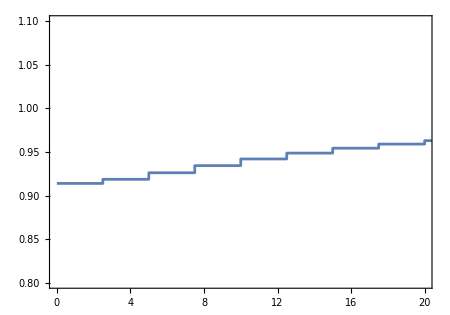

```mathematica
backplot=ListStepPlot[binnedRPAelossDataVSPT4,Right,PlotRange->{{0,20},{0.8,1.1}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]}]
```